## Set parameter values and define functions:

```mathematica
(*Seasonal forcing*)
beta[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

pC = (0.3)*(0.044); (*Probability of needing critical care*)
pH = (0.7)*(0.044); (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)

nuval = 1/(4.6/7); (*Rate of progressing to infectiousness*)
gammaval = 1/(5/7); (*Rate of losing infectiousness or going to the hospital*)

deltaHval = 1/(8/7); (*Rate of leaving hospital for those not going to critical care*)
deltaCval = 1/(6/7); (*Rate of leaving hospital and going to critical care*)
xiCval = 1/(10/7); (*Rate of leaving critical care*)

cfr = 0.01; (*Set overall case fatality rate*)
 
amplitude = 0.75; (*0.6*)
baseline = 1.75; (*1.4*)
phival= -3.8;

kappaval = 0.01;
importtime = N[(31+29+11)/7]; 
importlength = 0.5;

tmax = 2.5*52;

plotwindow = {0, 64};
plotwindowlong = {0, 52*2.5};
fs = 18;
imsz=400;

CCthreshold = 0.000089;
```

## Define model function:

```mathematica
runmodel[]:=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
cuminf'[t] == nuval*Eq[t],
cumhosp'[t] == gammaval*IHq[t] + gammaval*ICq[t],
cumcc'[t] == deltaCval*HCq[t],
cumm'[t]== 0.5*xiCval*CCq[t] + 0.078*deltaHval*HHq[t],
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>relaxtime, npi[t]-> 1-npifactorrelaxed],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1, cuminf[0]==0, cumhosp[0]==0, cumcc[0]==0, cumm[0]==0
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi, cuminf, cumhosp, cumcc, cumm},{t, 0, tmax}
];
```

## Run a scenario to test:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
relaxtime = npistart + 15/7;
npifactorrelaxed=0.2;
seasonality=0;
sol = runmodel[];
```

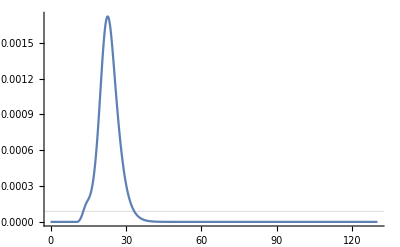

```mathematica
Plot[Evaluate[CCq[t]/.sol],{t,0,tmax}, PlotRange->All, GridLines->{{},{CCthreshold}}]
```

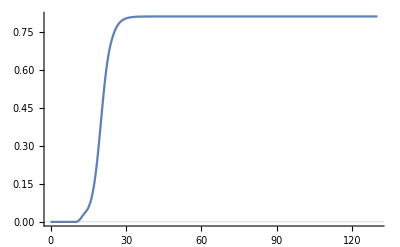

```mathematica
Plot[Evaluate[{cuminf[t]}/.sol],{t,0,tmax}, PlotRange->All, GridLines->{{},{CCthreshold}}]
```

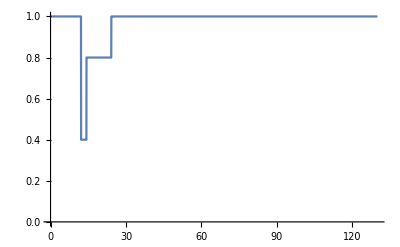

```mathematica
Plot[Evaluate[npi[t]/.sol],{t,0,tmax}, PlotRange->{0,1}, GridLines->{{},{CCthreshold}}]
```

## Run a bunch of scenarios and gather output:

```mathematica
seasonality = 0;
amplitude = 0;
npistart = importtime+2;
npifactor=0.6;
relaxtime = npistart + 15/7;
inf = {};
hosp = {};
crit = {};
mort = {};
Do[
Do[

npifactorrelaxed=0;
sol00r=runmodel[];
npifactorrelaxed=0.2;
sol02r=runmodel[];
npifactorrelaxed=0.4;
sol04r=runmodel[];
npifactorrelaxed=0.6;
sol06r=runmodel[];

itot00r = Table[(cuminf[npistart+w ]/.sol00r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
itot02r = Table[(cuminf[npistart+w ]/.sol02r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
itot04r = Table[(cuminf[npistart+w ]/.sol04r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
itot06r = Table[(cuminf[npistart+w ]/.sol06r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];

htot00r = Table[(cumhosp[npistart+w ]/.sol00r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
htot02r = Table[(cumhosp[npistart+w ]/.sol02r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
htot04r = Table[(cumhosp[npistart+w ]/.sol04r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
htot06r = Table[(cumhosp[npistart+w ]/.sol06r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];

ctot00r = Table[(cumcc[npistart+w ]/.sol00r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
ctot02r = Table[(cumcc[npistart+w ]/.sol02r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
ctot04r = Table[(cumcc[npistart+w ]/.sol04r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
ctot06r = Table[(cumcc[npistart+w ]/.sol06r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];

mtot00r = Table[(cumm[npistart+w ]/.sol00r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
mtot02r = Table[(cumm[npistart+w ]/.sol02r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
mtot04r = Table[(cumm[npistart+w ]/.sol04r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];
mtot06r = Table[(cumm[npistart+w ]/.sol06r)⟦1⟧, {w, {0,4,8,12,tmax-npistart}}];


inf = Join[inf, {Join[{baseline, npiend-npistart},Round[10000*Flatten[{itot06r, itot04r, itot02r, itot00r}ᵀ]]]}];
hosp = Join[hosp, {Join[{baseline, npiend-npistart},Round[10000*Flatten[{htot06r, htot04r, htot02r, htot00r}ᵀ],0.1]]}];
crit = Join[crit, {Join[{baseline, npiend-npistart},Round[10000*Flatten[{ctot06r, ctot04r, ctot02r, ctot00r}ᵀ],0.01]]}];
mort = Join[mort, {Join[{baseline, npiend-npistart},Round[10000*Flatten[{mtot06r, mtot04r, mtot02r, mtot00r}ᵀ],0.01]]}];

,{npiend, {npistart+4, npistart+8, npistart+12}}]
,{baseline,1.4, 3.4, 0.2}]
```

```mathematica
Join[{{"R0","Length","w0:none","w0:weak","w0:strong","w0:full","w4:none","w4:weak","w4:strong","w4:full","w8:none","w8:weak","w8:strong","w8:full","w12:none","w12:weak","w12:strong","w12:full","winf:none","winf:weak","winf:strong","winf:full"}},inf]//TableForm;
```

```mathematica
Join[{(*{"R0","Length","w0:none","w0:weak","w0:strong","w0:full","w4:none","w4:weak","w4:strong","w4:full","w8:none","w8:weak","w8:strong","w8:full","w12:none","w12:weak","w12:strong","w12:full","winf:none","winf:weak","winf:strong","winf:full"}*)},hosp]//TableForm;
```

```mathematica
Join[{(*{"R0","Length","w0:none","w0:weak","w0:strong","w0:full","w4:none","w4:weak","w4:strong","w4:full","w8:none","w8:weak","w8:strong","w8:full","w12:none","w12:weak","w12:strong","w12:full","winf:none","winf:weak","winf:strong","winf:full"}*)},crit]//TableForm;
```

```mathematica
Join[{(*{"R0","Length","w0:none","w0:weak","w0:strong","w0:full","w4:none","w4:weak","w4:strong","w4:full","w8:none","w8:weak","w8:strong","w8:full","w12:none","w12:weak","w12:strong","w12:full","winf:none","winf:weak","winf:strong","winf:full"}*)},mort]//TableForm;
```

## Plotting R0 = 1.4:

```mathematica
seasonality = 0;
amplitude = 0;
npistart = importtime+2;
npiend = npistart+4;
npifactor=0.6;
relaxtime = npistart + 15/7;
baseline = 1.4;

npifactorrelaxed = 0.6;
sol06 = runmodel[];

npifactorrelaxed = 0.4;
sol04 = runmodel[];

npifactorrelaxed = 0.2;
sol02 = runmodel[];

npifactorrelaxed = 0.0;
sol00 = runmodel[];
```

```mathematica
prmax = 1200;
```

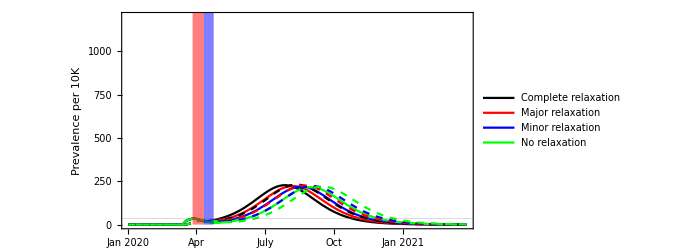

```mathematica
sf = 40;
fig14 = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol00],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol02],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol04],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol06],
sf * 10000*Evaluate[CCq[t]/.sol00],
sf * 10000*Evaluate[CCq[t]/.sol02],
sf * 10000*Evaluate[CCq[t]/.sol04],
sf * 10000*Evaluate[CCq[t]/.sol06],
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{Black, Red, Blue, Green, {Black, Dashed}, {Red, Dashed}, {Blue, Dashed}, {Green, Dashed}},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"Complete relaxation", "Major relaxation","Minor relaxation", "No relaxation"},AspectRatio->.5,
Epilog->{Red,Opacity[.5],Rectangle[{npistart,0},{npistart+15/7,5000}], 
Blue,Opacity[.5],Rectangle[{npistart+15/7,0},{npiend,5000}]}]
```

```mathematica
Export["~/Desktop/fig14_4.png", fig14];
```

## Plotting R0 = 2:

```mathematica
seasonality = 0;
amplitude = 0;
npistart = importtime+2;
npiend = npistart+4;
npifactor=0.6;
relaxtime = npistart + 15/7;
baseline = 2;

npifactorrelaxed = 0.6;
sol06 = runmodel[];

npifactorrelaxed = 0.4;
sol04 = runmodel[];

npifactorrelaxed = 0.2;
sol02 = runmodel[];

npifactorrelaxed = 0.0;
sol00 = runmodel[];
```

```mathematica
prmax = 1200;
```

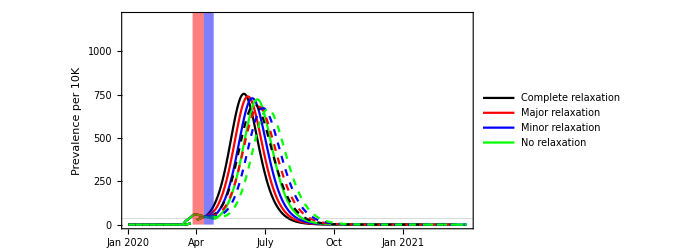

```mathematica
sf = 40;
fig20 = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol00],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol02],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol04],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol06],
sf * 10000*Evaluate[CCq[t]/.sol00],
sf * 10000*Evaluate[CCq[t]/.sol02],
sf * 10000*Evaluate[CCq[t]/.sol04],
sf * 10000*Evaluate[CCq[t]/.sol06],
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{Black, Red, Blue, Green, {Black, Dashed}, {Red, Dashed}, {Blue, Dashed}, {Green, Dashed}},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"Complete relaxation", "Major relaxation","Minor relaxation", "No relaxation"},AspectRatio->.5,
Epilog->{Red,Opacity[.5],Rectangle[{npistart,0},{npistart+15/7,5000}], 
Blue,Opacity[.5],Rectangle[{npistart+15/7,0},{npiend,5000}]}]
```

```mathematica
Export["~/Desktop/fig20_4.png", fig20];
```

## Plotting R0 = 2.4:

```mathematica
seasonality = 0;
amplitude = 0;
npistart = importtime+2;
npiend = npistart+4;
npifactor=0.6;
relaxtime = npistart + 15/7;
baseline = 2.4;

npifactorrelaxed = 0.6;
sol06 = runmodel[];

npifactorrelaxed = 0.4;
sol04 = runmodel[];

npifactorrelaxed = 0.2;
sol02 = runmodel[];

npifactorrelaxed = 0.0;
sol00 = runmodel[];
```

```mathematica
prmax = 1200;
```

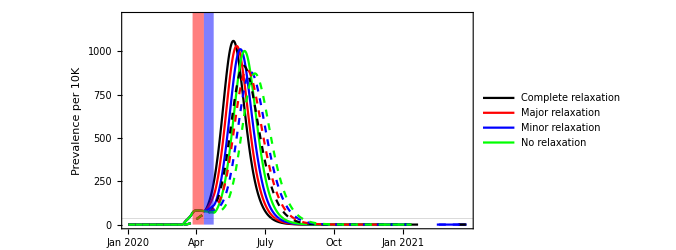

```mathematica
sf = 40;
fig24 = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol00],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol02],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol04],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol06],
sf * 10000*Evaluate[CCq[t]/.sol00],
sf * 10000*Evaluate[CCq[t]/.sol02],
sf * 10000*Evaluate[CCq[t]/.sol04],
sf * 10000*Evaluate[CCq[t]/.sol06],
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{Black, Red, Blue, Green, {Black, Dashed}, {Red, Dashed}, {Blue, Dashed}, {Green, Dashed}},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"Complete relaxation", "Major relaxation","Minor relaxation", "No relaxation"},AspectRatio->.5,
Epilog->{Red,Opacity[.5],Rectangle[{npistart,0},{npistart+15/7,5000}], 
Blue,Opacity[.5],Rectangle[{npistart+15/7,0},{npiend,5000}]}]
```

```mathematica
Export["~/Desktop/fig24_4.png", fig24];
```